All examples below use data from two samples tablets (X202071 and X202470).

Get the number of observations:

```mathematica
Length[obsData]
```

236

The types of observations:

```mathematica
obsData[Counts/*ReverseSort,"Type"]
```

An example observation:

```mathematica
Normal[obsData[22]]
```

<|Type→RelativePosition,Content→<|Object→Moon,Reference→Spica,Displacements→{{<|Cubits→4,Fingers→Missing[Unmentioned],TotalCubits→4,IdealDegrees→8,RealDegrees→9.08|>,Below},Missing[Destroyed]}|>,Date→<|JulianDate→<|Year→-207,Month→4,Day→15|>,BabylonianDate→<|Year→{SE,104},Month→I,Day→13|>,Time→BeginningOfTheNight,DateObject→Day: Thu 15 Apr -208 (Juliancalendar)|>,Provenance→<|Creator→Christopher Wolfram,TabletID→X202071,LineNumber→8,Notes→Missing[]|>|>

Get the number of observations by month (for the two sample tablets):

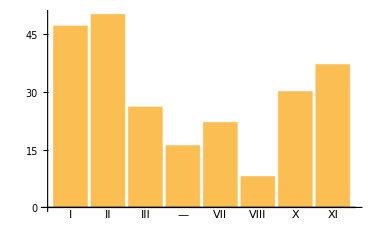

```mathematica
obsData[Counts/*(BarChart[#,ChartLabels->Automatic]&),"Date","BabylonianDate","Month"]
```

Use JPL ephemerides to calculate the real positions of synodic objects and references in observations of relative position:

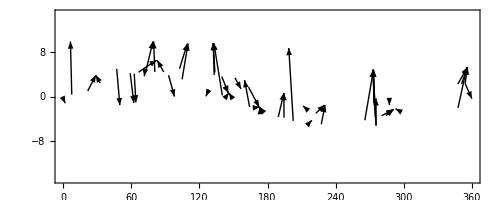

```mathematica
Module[{obs,lines,paths},
obs=Normal[obsData[Select[#Type==="RelativePosition"&],{Query["Content",{"Object","Reference"}],Query["Date","DateObject"]}]];
lines={DiaryAstronomicalPosition[#1["Object"],#2],DiaryAstronomicalPosition[#1["Reference"],#2]}&@@@obs;
paths=Arrow@*GeoPath/@Map[GeoPosition@*Reverse,DeleteMissing[lines,1,2],{2}];
GeoGraphics[{Arrowheads[Small],paths},GeoBackground->White,GeoRange->{{-15,15},{0,360}},Frame->True]
]
```

Observation type by time of day:

```mathematica
obsData[GroupBy[Query["Date","Time"]]/*KeySelect[Not@*MissingQ],Counts/*ReverseSort,"Type"]
```

Mean observations per day (only for dated observations):

```mathematica
N@obsData[Counts/*Mean,"Date","BabylonianDate"]
```

2.18519

More examples are available at the end of the Format Discussion.